```mathematica
(* Set parameters *)
```

```mathematica
(* Set values of power laws *)
taumin=1;
taumax=2.5;
taustep=.5;
```

```mathematica
(* set number of trials (sample size),
number of nodes in the graph,
values of exponential cutoff *)
trials=100;
n=10000;
cutoff=10^-5;
pts=9;
kmax=30;
kmin=1;
logstep=(kmax/kmin)^(1/(pts-1));
```

```mathematica
(* Numerical simulations here! *)
```

```mathematica
Do[
Print["τ = ", tau];
Clear[data];
data={};
kappa = kmin;
While[kappa≤kmax,
(* Generate a matrix containing degree sequences:
each row corresponds to a specific realization of the 
random degree sequence; there are `trials' rows *)
sequences=
Table[
Module[{sum,degrees},
sum=1;
(* Generate array of degrees; sum must be even *)
While[OddQ[sum],
Clear[degrees];
degrees = Parallelize[Table[
Module[{x, check}, 
check = 0;
While[check != 1,
x = IntegerPart[(-kappa)*Log[1 - RandomReal[]]];
If[RandomReal[] < (x + cutoff)^(-tau), check = 1]
];
x]
, {i, 1, n}]];
sum=Total[degrees];
];
degrees
],{k,1,trials}];

(* Generate graphs with the specified degree sequences;
g contains all the 'trials' graphs *)
g=Parallelize[Table[RandomGraph[DegreeGraphDistribution[sequences[[i]]]],{i,trials}]];

(* list the size of the largest components of each graph *)
biggest=Table[Length[First[ConnectedComponents[g[[i]]]]]/n,{i,trials}];

(* For each 'kappa' calculate mean and variance of the (relative) size of the largest component
over the 'trials' graphs and store in a table *)
data=Append[data,{N[kappa],N[Mean[biggest]],N[Sqrt[Variance[biggest]/n]]}];

Print["κ = ",N[kappa],"; relative size = ", N[Mean[biggest]], "; Error = ", N[Sqrt[Variance[biggest]/n]]];
kappa*=logstep];

(* Write on file the results: a file for each value of 'tau' *)
Export["~/Codello/graphs/main/output/giant_nodes="<>ToString[IntegerPart[N[n]]]<>"_tau="<>ToString[N[tau,2]]<>".dat",data]

,{tau,taumin,taumax,taustep}]
```

τ = 1.

κ = 1.; relative size = 0.002718; Error = 8.90169×10^-6

κ = 1.52982; relative size = 0.047638; Error = 0.000215444

κ = 2.34035; relative size = 0.303515; Error = 0.000100235

κ = 3.58031; relative size = 0.469166; Error = 0.0000766087

κ = 5.47723; relative size = 0.576934; Error = 0.0000617594

κ = 8.37917; relative size = 0.648681; Error = 0.0000507529

κ = 12.8186; relative size = 0.699348; Error = 0.000047298

κ = 19.6102; relative size = 0.737403; Error = 0.0000460786

κ = 30.; relative size = 0.766337; Error = 0.0000511201

τ = 1.5

κ = 1.; relative size = 0.001541; Error = 4.02541×10^-6

κ = 1.52982; relative size = 0.005425; Error = 0.0000191218

κ = 2.34035; relative size = 0.092368; Error = 0.000251384

κ = 3.58031; relative size = 0.286451; Error = 0.000106461

κ = 5.47723; relative size = 0.410757; Error = 0.0000858721

κ = 8.37917; relative size = 0.495021; Error = 0.0000748341

κ = 12.8186; relative size = 0.552297; Error = 0.0000666041

κ = 19.6102; relative size = 0.595722; Error = 0.000058161

κ = 30.; relative size = 0.625141; Error = 0.0000514291

τ = 2.

κ = 1.; relative size = 0.00107; Error = 2.29844×10^-6

κ = 1.52982; relative size = 0.002194; Error = 6.46017×10^-6

κ = 2.34035; relative size = 0.006599; Error = 0.0000280229

κ = 3.58031; relative size = 0.07294; Error = 0.000266667

κ = 5.47723; relative size = 0.205199; Error = 0.000156071

κ = 8.37917; relative size = 0.301227; Error = 0.000112414

κ = 12.8186; relative size = 0.369143; Error = 0.0000995163

κ = 19.6102; relative size = 0.419454; Error = 0.0000892559

κ = 30.; relative size = 0.452898; Error = 0.0000742923

τ = 2.5

κ = 1.; relative size = 0.000843; Error = 1.68927×10^-6

κ = 1.52982; relative size = 0.001346; Error = 3.0031×10^-6

κ = 2.34035; relative size = 0.002579; Error = 7.54421×10^-6

κ = 3.58031; relative size = 0.005807; Error = 0.0000264209

κ = 5.47723; relative size = 0.019858; Error = 0.000123871

κ = 8.37917; relative size = 0.086449; Error = 0.000233537

κ = 12.8186; relative size = 0.154588; Error = 0.000151859

κ = 19.6102; relative size = 0.203015; Error = 0.000151663

κ = 30.; relative size = 0.239935; Error = 0.000145782

τ = 3.

κ = 1.; relative size = 0.000698; Error = 1.52408×10^-6

κ = 1.52982; relative size = 0.000989; Error = 2.27811×10^-6

κ = 2.34035; relative size = 0.001453; Error = 4.11318×10^-6

κ = 3.58031; relative size = 0.002209; Error = 6.47153×10^-6

κ = 5.47723; relative size = 0.003789; Error = 0.0000135056

κ = 8.37917; relative size = 0.006827; Error = 0.0000305782

κ = 12.8186; relative size = 0.010774; Error = 0.0000634819

κ = 19.6102; relative size = 0.022158; Error = 0.000137342

κ = 30.; relative size = 0.038489; Error = 0.000166318

```mathematica
(* Plot points with errorbars *)
```

```mathematica
Clear[data];
data=Table[
Import["~/Codello/graphs/main/output/giant_nodes="<>ToString[IntegerPart[N[n]]]<>"_tau="<>ToString[N[tau,2]]<>".dat","Table"]
,{tau,taumin,taumax,taustep}];
```

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
plotanalytic=LogLinearPlot[x,{x,1,30}];
plotpoints=ErrorListLogLinearPlot[data,PlotStyle->Table[ColorData["DarkRainbow",(taumax-x)/(taumax-taumin)],{x,taumin,taumax,taustep}]]
```

```mathematica
(* Analytic results here *)
```

```mathematica
plots=Table[
Module[{gendeg,avg,genexc,temp,k,p},
Subscript[p, k]=UnitStep[k-.5] k^-tau E^(-k/kappa); Subscript[p, k] = Subscript[p, k]/Sum[Subscript[p, k],{k,0,∞}];
(* Definition of the generating functions of the distributions *)
gendeg=GeneratingFunction[Subscript[p, k],k,z]//FullSimplify;
avg=D[gendeg,z]/.z->1;
temp=D[gendeg,z]/avg;
genexc[z_?NumericQ,kappa_]:=temp//FullSimplify;
Print["τ = ",N[tau,2],"; Degree gen func = ", gendeg, "; Exc deg gen func = ", D[gendeg,z]/avg];
P[kappa_?NumericQ]:=
1-gendeg/.FindRoot[z-genexc[z,kappa],{z,0.0001,0,1}]//Quiet;
LogLinearPlot[P[kappa],{kappa,kmin,kmax},PlotRange->{{kmin,kmax},{0,1}},PlotStyle->ColorData["DarkRainbow",(taumax-tau)/(taumax-taumin)]]
]
,{tau,taumin,taumax,taustep}]
```

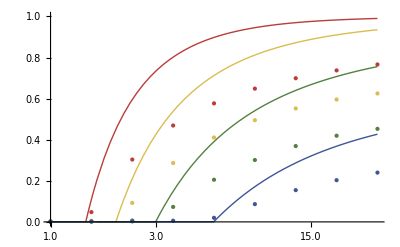

```mathematica
Show[plots,plotpoints]
```